```mathematica
F[x,y,h]=(h x)/(√(a^2-h^2))+y-h
```

-h+(h x)/(√(a^2-h^2))+y

```mathematica
Solve[{F[x,y,h]==0,D[F[x,y,h],h]==0},{x,y}]
```

{{x→((a^2-h^2)^(3/2))/a^2,y→h^3/a^2}}

```mathematica
Integrate[Cos[x]^a Sin[x]^b,{x,0,Pi/2},Assumptions->a∈Integers&&b∈Integers]
```

ConditionalExpression[(Gamma[(1+a)/2] Gamma[(1+b)/2])/(2 Gamma[1/2 (2+a+b)]), a≥0&&b≥0]

```mathematica
(Gamma[(1+a)/2] Gamma[(1+b)/2])/(2 Gamma[1/2 (2+a+b)])/.{a->2,b->4}
```

π/32

```mathematica
l=√(a^2-h^2 Sin[ϕ]^2)-h Cos[ϕ];
k=(l Sin[ϕ])/(l Cos[ϕ]-h);
G[x_,y_,h_]:=k x-y-k h/.{ϕ->Pi/4}
```

```mathematica
G[x,y,h]//Simplify
```

(h^2-h (√(2 a^2-h^2)+x-3 y)+√(2 a^2-h^2) (x-y))/(-3 h+√(2 a^2-h^2))

```mathematica
Solve[{G[x,y,h]==0,D[G[x,y,h],h]==0},{x,y}]
```

{{x→-(((h (-h/(√2)+√(a^2-h^2/2)) (-1+(-1/(√2)-h/(2 √(a^2-h^2/2)))/(√2)))/(√2 (-h+(-h/(√2)+√(a^2-h^2/2))/(√2))^2)-(h (-1/(√2)-h/(2 √(a^2-h^2/2))))/(√2 (-h+(-h/(√2)+√(a^2-h^2/2))/(√2)))-(-h/(√2)+√(a^2-h^2/2))/(√2 (-h+(-h/(√2)+√(a^2-h^2/2))/(√2))))/(-((-h/(√2)+√(a^2-h^2/2)) (-1+(-1/(√2)-h/(2 √(a^2-h^2/2)))/(√2)))/(√2 (-h+(-h/(√2)+√(a^2-h^2/2))/(√2))^2)+(-1/(√2)-h/(2 √(a^2-h^2/2)))/(√2 (-h+(-h/(√2)+√(a^2-h^2/2))/(√2))))),y→-((8 a^4 h+4 a^2 h^3-4 h^5-a^4 √(2 a^2-h^2)-10 a^2 h^2 √(2 a^2-h^2)+3 h^4 √(2 a^2-h^2))/(a^2 (-3 h+√(2 a^2-h^2))^2))}}

```mathematica
Simplify@%
```

{{x→1/2 (-2 h+√(2 a^2-h^2)+(h^2 (2 h+√(2 a^2-h^2)))/a^2),y→(h^4 (4 h-3 √(2 a^2-h^2))+a^4 (-8 h+√(2 a^2-h^2))+2 a^2 h^2 (-2 h+5 √(2 a^2-h^2)))/(a^2 (-3 h+√(2 a^2-h^2))^2)}}

```mathematica
Apart@%
```

{{x→-h+h^3/a^2+1/2 √(2 a^2-h^2)+(h^2 √(2 a^2-h^2))/(2 a^2),y→-h+h^3/(2 a^2)+1/2 √(2 a^2-h^2)}}

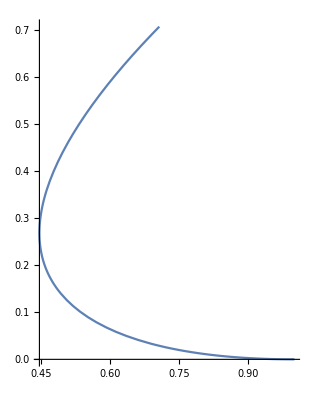

```mathematica
ParametricPlot[{-h+h^3+(√(2-h^2))/2+1/2 h^2 √(2-h^2),-h+h^3/2+(√(2-h^2))/2},{h,0,1}]
```

```mathematica
D[-h+h^3+(√(2-h^2))/2+1/2 h^2 √(2-h^2),h]
```

-1+3 h^2-h/(2 √(2-h^2))-h^3/(2 √(2-h^2))+h √(2-h^2)

```mathematica
Solve[-1+3 h^2-h/(2 √(2-h^2))-h^3/(2 √(2-h^2))+h √(2-h^2)==0,h]
```

{{h→1/(√5)},{h→-√(1/6 (7-√17))},{h→√(1/6 (7+√17))}}

```mathematica
x[h_]:=-h+h^3+(√(2-h^2))/2+1/2 h^2 √(2-h^2);
y[h_]:=-h+h^3/2+(√(2-h^2))/2;
```

```mathematica
x[1/√5]
```

```mathematica
1/(√5)//N
```

0.447214